## NF Theory for reaction-diffusion equations with 10 components

```mathematica
SetDirectory["/home/shubham/Dropbox/Shubham/Turing_submission/Code/"];
```

```mathematica
sparseJ=Import["data_TuringLargeNetwork/SparseJacobian.dat","Table"];
```

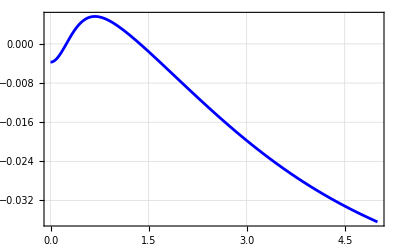

```mathematica
dS2=DiagonalMatrix[{0,0.05,0,1.,2.,0,0,0,0,0}];
Plot[Max[Re[Eigenvalues[sparseJ-k^2dS2]]],{k,0,5},PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Blue]
```

#### Numerical solution of PDEs

```mathematica
n=10;
u=Table[Symbol["u"<>ToString[i]][t,x],{i,1,n}];
```

```mathematica
δ=10;
eqn=Table[1/δ D[u[[i]],{t,1}]==(sparseJ.u)[[i]]+(dS2.Table[D[u[[i]],{x,2}],{i,n}])[[i]]-0.05u[[i]]^3,{i,n}];
```

```mathematica
ic=Flatten[{u1[0,x]==0.01(Cos[x]+Cos[2x]),Table[Symbol["u"<>ToString[i]][0,x]==0,{i,2,n}]}];
```

```mathematica
bc=Table[Symbol["u"<>ToString[i]][t,Pi]==Symbol["u"<>ToString[i]][t,-Pi],{i,1,n}];
```

```mathematica
T=200;
```

```mathematica
sol=NDSolveValue[Flatten[{eqn,ic,bc}],Table[Symbol["u"<>ToString[i]],{i,n}],{t,0,2000},{x,-Pi,Pi}];
```

```mathematica
frames=Table[Plot[{sol[[8]][t,x]},{x,-Pi,Pi},PlotRange->{-0.4,0.4},PlotStyle->{{Thick,Red},{Thick,Green},{Thick,Blue}}],{t,0,T,5}];
ListAnimate[frames]
```

#### NF Fit

```mathematica
z=Table[1/Pi NIntegrate[Cos[1x]sol[[8]][t,x],{x,-Pi,Pi},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->5],{t,0,T}];
times=Table[i,{i,Dimensions[z][[1]]}];
ztofit=Table[{times[[i]],z[[i]]},{i,Dimensions[z][[1]]}];
```

```mathematica
rsol=DSolve[{r'[x]==p1 r[x]-p2 r[x]^3,r[0]==r0},r[x],x,Assumptions->{r0>0,p1>0,p2>0}]//Quiet//FullSimplify;
```

```mathematica
functofit=r[x]/.rsol[[1,1]]
```

(ⅇ^(p1 x) √p1 r0)/(√(p1-p2 r0^2) √(1+(ⅇ^(2 p1 x) p2 r0^2)/(p1-p2 r0^2)))

```mathematica
fit=NonlinearModelFit[ztofit,functofit,{{r0,0.1},{p1,0.1},{p2,0.1}},x]
```

FittedModel[…]

```mathematica
param=fit["BestFitParameters"]
```

{r0→0.00232415,p1→0.0388403,p2→0.367139}

```mathematica
plt=Plot[functofit/.param,{x,0,200},PlotStyle->{Thick,Red}];
simIn=ListLinePlot[Re[z],PlotStyle->{Thick,Dashed,Blue}];
```

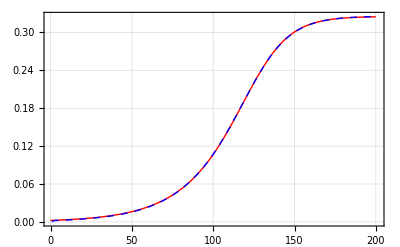

```mathematica
rdynu8=Show[{plt,simIn},PlotRange->All,BaseStyle->{FontFamily->"CMU Serif",14},Frame->True,GridLines->Automatic]
```

```mathematica
z1t=functofit/.x->t/.param
```

(0.00232421 ⅇ^(0.0388403 t))/(√(1+0.0000510619 ⅇ^(0.0776806 t)))

```mathematica
{t1,t2,t3}={100,120,200}
```

{100,120,200}

#### Fitting to pattern in physical space

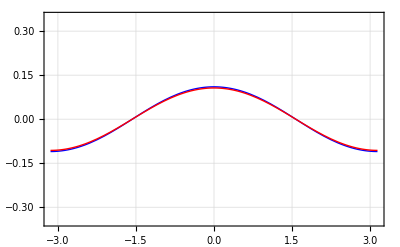

```mathematica
u8plt1=Plot[{sol[[8]][t,x]/.t->t1,z1t Cos[x]-0.3z1t^3Cos[3x]/.t->t1},{x,-Pi,Pi},PlotRange->{-0.35,0.35},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

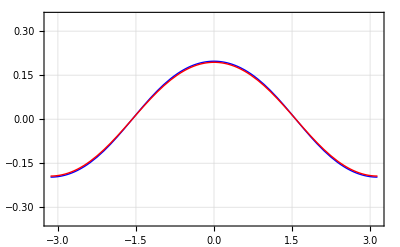

```mathematica
u8plt2=Plot[{sol[[8]][t,x]/.t->t2,z1t Cos[x]-0.3z1t^3Cos[3x]/.t->t2},{x,-Pi,Pi},PlotRange->{-0.35,0.35},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

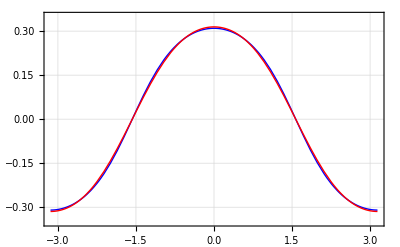

```mathematica
u8plt3=Plot[{sol[[8]][t,x]/.t->t3,z1t Cos[x]-0.3z1t^3Cos[3x]/.t->t3},{x,-Pi,Pi},PlotRange->{-0.35,0.35},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

#### Rotation

```mathematica
ω=Pi/6;
```

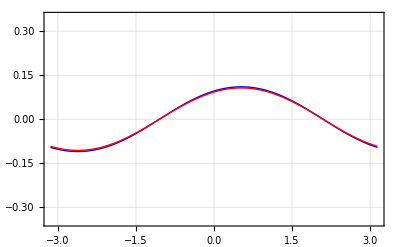

```mathematica
u8plt1=Plot[{sol[[8]][t,x]/.t->t1/.x->Mod[y-ω,2 Pi,-Pi],z1t Cos[x]-0.3z1t^3Cos[3x]/.t->t1/.x->Mod[y-ω,2 Pi,-Pi]},{y,-Pi,Pi},PlotRange->{-0.35,0.35},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

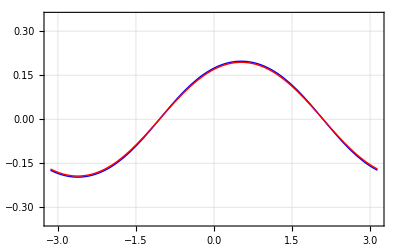

```mathematica
u8plt2=Plot[{sol[[8]][t,x]/.t->t2/.x->Mod[y-ω,2 Pi,-Pi],z1t Cos[x]-0.3z1t^3Cos[3x]/.t->t2/.x->Mod[y-ω,2 Pi,-Pi]},{y,-Pi,Pi},PlotRange->{-0.35,0.35},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

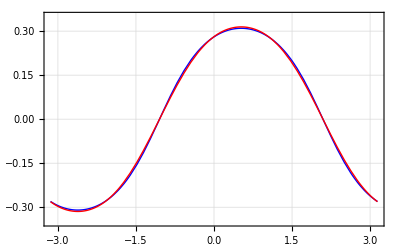

```mathematica
u8plt3=Plot[{sol[[8]][t,x]/.t->t3/.x->Mod[y-ω,2 Pi,-Pi],z1t Cos[x]-0.3z1t^3Cos[3x]/.t->t3/.x->Mod[y-ω,2 Pi,-Pi]},{y,-Pi,Pi},PlotRange->{-0.35,0.35},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

#### Similar NF procedure to for second component

```mathematica
z=Table[-1/Pi NIntegrate[Cos[1x]sol[[2]][t,x],{x,-Pi,Pi},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->5],{t,0,T}];
```

```mathematica
times=Table[i,{i,Dimensions[z][[1]]}];
ztofit=Table[{times[[i]],z[[i]]},{i,Dimensions[z][[1]]}];
```

```mathematica
rsol=DSolve[{r'[x]==p1 r[x]-p2 r[x]^3,r[0]==r0},r[x],x,Assumptions->{r0>0,p1>0,p2>0}]//Quiet//FullSimplify;
```

```mathematica
functofit=r[x]/.rsol[[1,1]]
```

(ⅇ^(p1 x) √p1 r0)/(√(p1-p2 r0^2) √(1+(ⅇ^(2 p1 x) p2 r0^2)/(p1-p2 r0^2)))

```mathematica
fit=NonlinearModelFit[ztofit,functofit,{{r0,0.1},{p1,0.1},{p2,0.1}},x]
```

FittedModel[(«22» ⅇ^(«1»))/(√(1+«23» ⅇ^(«1»)))]

```mathematica
param=fit["BestFitParameters"]
```

{r0→0.000820356,p1→0.0388411,p2→2.91328}

```mathematica
plt=Plot[functofit/.param,{x,0,200},PlotStyle->{Thick,Red}];
simIn=ListLinePlot[Re[z],PlotStyle->{Thick,Dashed,Blue}];
```

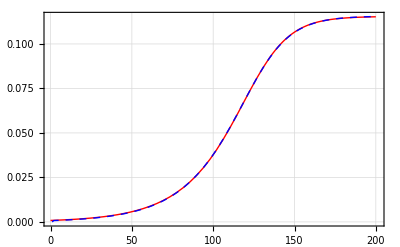

```mathematica
rdynu2=Show[{plt,simIn},PlotRange->All,BaseStyle->{FontFamily->"CMU Serif",14},Frame->True,GridLines->Automatic]
```

```mathematica
z1t=functofit/.x->t/.param
```

-(0.000820376 ⅇ^(0.0388411 t))/(√(1+0.0000504797 ⅇ^(0.0776822 t)))

```mathematica
{t1,t2,t3}={100,120,200}
```

{100,120,200}

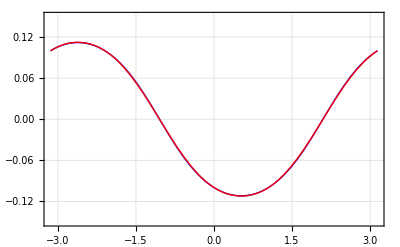

```mathematica
u2plt3=Plot[{sol[[2]][t,x]/.t->t3/.x->Mod[y-ω,2 Pi,-Pi],z1t Cos[x]-2z1t^3Cos[3x]/.t->t3/.x->Mod[y-ω,2 Pi,-Pi]},{y,-Pi,Pi},PlotRange->{-0.15,0.15},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

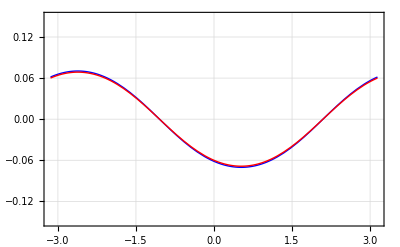

```mathematica
u2plt2=Plot[{sol[[2]][t,x]/.t->t2/.x->Mod[y-ω,2 Pi,-Pi],z1t Cos[x]-2z1t^3Cos[3x]/.t->t2/.x->Mod[y-ω,2 Pi,-Pi]},{y,-Pi,Pi},PlotRange->{-0.15,0.15},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

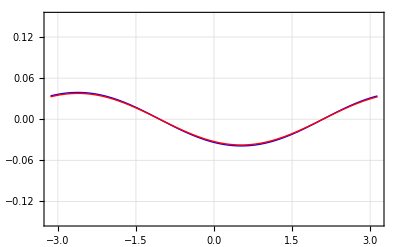

```mathematica
u2plt1=Plot[{sol[[2]][t,x]/.t->t1/.x->Mod[y-ω,2 Pi,-Pi],z1t Cos[x]-0.3z1t^3Cos[3x]/.t->t1/.x->Mod[y-ω,2 Pi,-Pi]},{y,-Pi,Pi},PlotRange->{-0.15,0.15},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

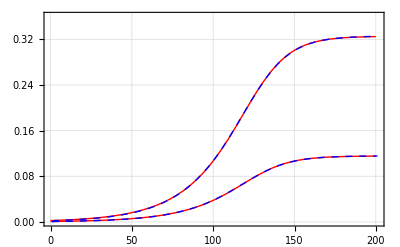

```mathematica
rdyn=Show[rdynu2,rdynu8,PlotRange->{0,0.36}]
```

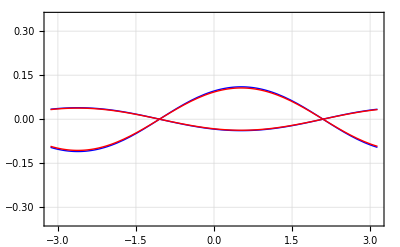

```mathematica
largenet1=Show[u2plt1,u8plt1,PlotRange->{-0.35,0.35}]
```

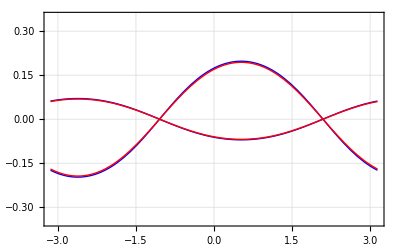

```mathematica
largenet2=Show[u2plt2,u8plt2,PlotRange->{-0.35,0.35}]
```

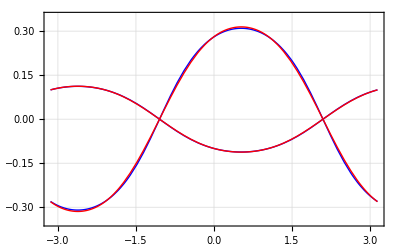

```mathematica
largenet3=Show[u2plt3,u8plt3,PlotRange->{-0.35,0.35}]
```